1/(k+b s+m s^2)

1/(10+5 ⅈ w-10 w^2)

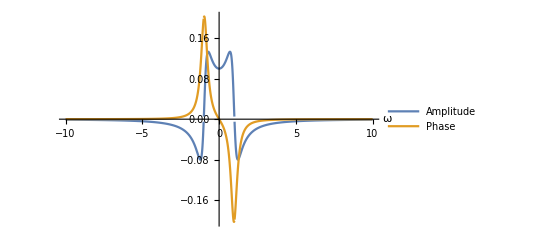

```mathematica
transfer = 1/(s^2 *  m + k +s*b)
transferfunc[w] = transfer/. {s -> Sqrt[-1]*w, m-> 10, b -> 5, k->10}
Plot[{Tooltip@Re@transferfunc[w],Tooltip@Im@transferfunc[w]},{w,-10,10},PlotStyle->Thick,PlotRange->All, PlotLegends->{"Amplitude","Phase"}, AxesLabel->{"ω"}]
```

```mathematica
(*Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20}]*)
```

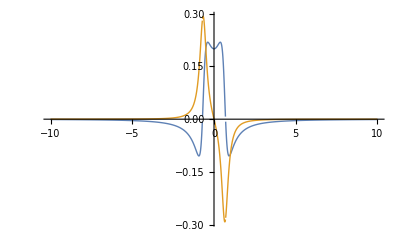

```mathematica
(* Manipulate[Plot[{Tooltip@Re@exp1,Tooltip@Im@exp1},{w,-10,10},PlotStyle->Thick,PlotRange->All], {k,0,10},{m,0,10}, {b,0,10}]*)

Plot[{Tooltip@Re@transferfunc[w],Tooltip@Im@transferfunc[w]},{w,-10,10},PlotStyle->Thick,PlotRange->All]
```